```mathematica
Clear["Global`*"];
ssx1i={};
ssx1d={};
ssx2i={};
ssx2d={};
ssx3i={};
ssx3d={};
ssx4i={};
ssx4d={};
ssx5i={};
ssx5d={};
ssx6i={};
ssx6d={};
ssin={};
(* Initialize all the equations and parameters *)
sTot=6.943934962;eTot=5.306064244;
dEs={D[x1[t],t]==-k1*x1[t]*x3[t]-k4*x1[t]*x4[t]+k2*x5[t]+k5*x6[t]+k7*x2[t],D[x2[t],t]==k3*x5[t]+k6*x6[t]-k7*x2[t],D[x3[t],t]==-k1*x1[t]*x3[t]+k2*x5[t]+k3*x5[t]-k8*x3[t]+k9*x4[t],D[x4[t],t]==-k4*x1[t]*x4[t]+k5*x6[t]+k6*x6[t]+k8*x3[t]-k9*x4[t],D[x5[t],t]==k1*x1[t]*x3[t]-k2*x5[t]-k3*x5[t]-k10*x5[t]+k11*x6[t],D[x6[t],t]==k4*x1[t]*x4[t]-k5*x6[t]-k6*x6[t]+k10*x5[t]-k11*x6[t]};
invaEs={x1[t]+x2[t]+x5[t]+x6[t]==sTot,x3[t]+x4[t]+x5[t]+x6[t]==eTot};
(*params = {k1->184.8681819,k2->0.01489431477,k3->177.5280007,k4->60.26409666,k5->1.873817423,k6->0.2608688883,k7->1.57210279,k8->0.02405645734,k9->1.411107556,k10->82.77297468,k11->0.02087603873};*)
(* Get the steady state first *)
tf=50000;
input=4;
icEs={x1[0]==sTot,x2[0]==0,x3[0]==input,x4[0]==0,x5[0]==0,x6[0]==0};
params = {k1->184.8681819,k2->0.01489431477,k3->177.5280007,k4->60.26409666,k5->1.873817423,k6->0.2608688883,k7->1.57210279,k8->0.02405645734,k9->1.411107556,k10->82.77297468,k11->0.02087603873};

sol=NDSolve[{dEs,icEs}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

(*newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};*)

For[i=0,i≤300,i++,
tf=50000;
(*newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]]+0.1*i,x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};*)
newIC={x1[0]==sTot,x2[0]==0,x3[0]==4+i*0.01,x4[0]==0,x5[0]==0,x6[0]==0};
sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

ssx1i=Append[ssx1i,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2i=Append[ssx2i,Evaluate[x2[tf]/.sol][[1]]];ssx3i=Append[ssx3i,Evaluate[x3[tf]/.sol][[1]]];ssx4i=Append[ssx4i,Evaluate[x4[tf]/.sol][[1]]];ssx5i=Append[ssx5i,Evaluate[x5[tf]/.sol][[1]]];ssx6i=Append[ssx6i,Evaluate[x6[tf]/.sol][[1]]]
];

For[i=0,i≤300,i++,
tf=50000;
(*newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]]-i*0.1,x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};*)
newIC={x1[0]==sTot,x2[0]==0,x3[0]==7-i*0.01,x4[0]==0,x5[0]==0,x6[0]==0};
sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

(*If[Abs[Evaluate[x1'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x1''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6''[tf]/.sol][[1]]]≤0.001,*) 
ssx1d=Append[ssx1d,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2d=Append[ssx2d,Evaluate[x2[tf]/.sol][[1]]];ssx3d=Append[ssx3d,Evaluate[x3[tf]/.sol][[1]]];ssx4d=Append[ssx4d,Evaluate[x4[tf]/.sol][[1]]];ssx5d=Append[ssx5d,Evaluate[x5[tf]/.sol][[1]]];ssx6d=Append[ssx6d,Evaluate[x6[tf]/.sol][[1]]]
(*];*)
];
```

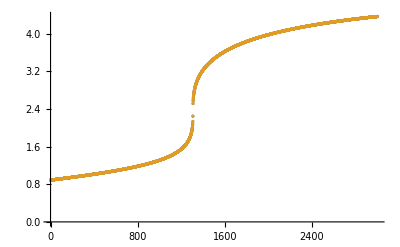

```mathematica
ListPlot[{ssx2i,Reverse[ssx2d]},PlotRange->Full]
```

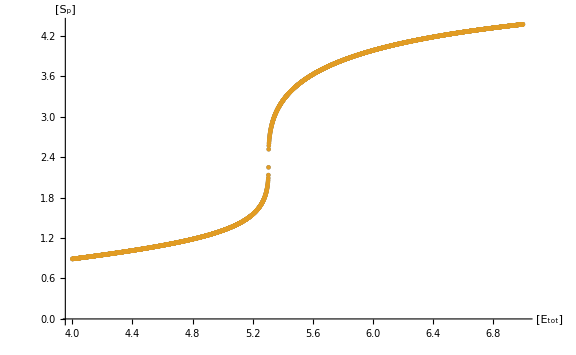

```mathematica
ListPlot[{Transpose@{Range[4,7,0.001],ssx2i},Transpose@{Range[4,7,0.001],Reverse[ssx2d]}},AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["E","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]"}]]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->All]
```

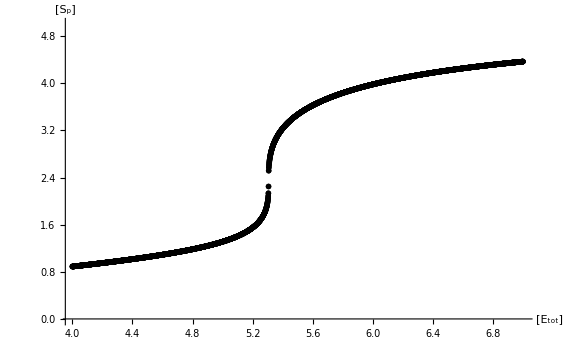

```mathematica
ListPlot[{Transpose@{Range[4,7,0.001],ssx2i},Transpose@{Range[4,7,0.001],Reverse[ssx2d]}},PlotTheme->"Monochrome",AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["E","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]"}]]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->{0,5}]
```

```mathematica
Ticks->{{4,7,1},{0,1,0.2}}
```

Ticks→{{4,7,1},{0,1,0.2}}

```mathematica
PlotRange->{0,sTot}
```

PlotRange→{0,6.94393}

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

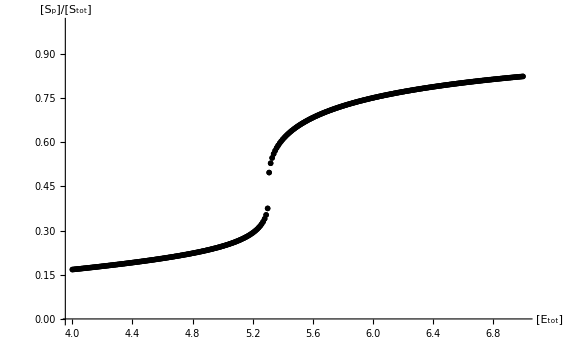

```mathematica
ListPlot[{Transpose@{Range[4,7,0.01],ssx2i/eTot},Transpose@{Range[4,7,0.01],Reverse[ssx2d/eTot]}},PlotTheme->"Monochrome",AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["E","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->{0,1}]
```